```mathematica
(*
Set up the simulation properties
*)
xMin=0;
xMax=100;
LL=xMax-xMin;
NN=512;
(*
Get an array of x-values that span the area in which we are interested
*)
xArray={};
Do[AppendTo[xArray,N[xx]],{xx,xMin,xMax-LL/NN/2,LL/NN}];
Length[xArray]
```

512

```mathematica
(*
Set up a gaussian wave packet
*)
k0=10;
x0=(xMin+xMax)*.3;
m=510998.90984764067; (* eV / c^2 *)
ℏ=0.6582118991312933; (* eV fs *)
c=299.792458; (* nm / fs *)
ℏc=197.3269631254185;(* eV fs c *)
a=1.5;
τ=2*m*a^2/ℏc;
Ψ0[x_]:=Simplify[
(Sqrt[2*Pi]*a)^(-1/2)*Exp[I*k0*(x-x0)]*Exp[-(x-x0)^2/(4*a^2)]];
(*Ψ0[x_]:=Simplify[
(Sqrt[2*Pi]*a)^(-1/2)*Exp[I*k0*x]*Exp[-x^2/(4*a^2)]];*)
(*Ψ0[x_]:=Exp[-(x-LL/2)^2/(4*.04*LL)+I*500/LL*x]*)
Ψ0Abs2[x_]=Abs[Ψ0[x]]^2;
Integrate[Ψ0Abs2[x],{x,xMin,xMax}]
```

1.

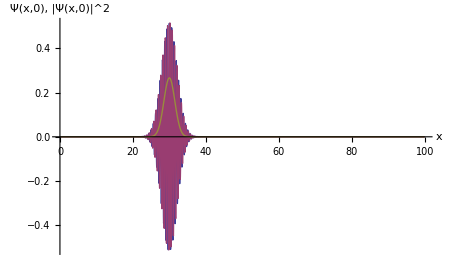

```mathematica
Plot[
{Re[Ψ0[x]],Im[Ψ0[x]],Ψ0Abs2[x]},
{x,xMin,xMax},
PlotRange->All,
AxesLabel->{"x","Ψ(x,0), |Ψ(x,0)|^2"}
]
```

```mathematica
(*
Save the wave packet numerically in an array
*)
Ψ0Array=Ψ0[xArray];
Ψ0Abs2Array=Ψ0Abs2[xArray];
Sum[Ψ0Abs2Array[[i]],{i,1,NN}]*(LL/NN)

NumberForm[Ψ0[xArray[[150]]],32]
NumberForm[Ψ0Array[[150]],32]
```

1.

-0.4264866663801281-0.2009916044119778 ⅈ

-0.4264866663801281-0.2009916044119778 ⅈ

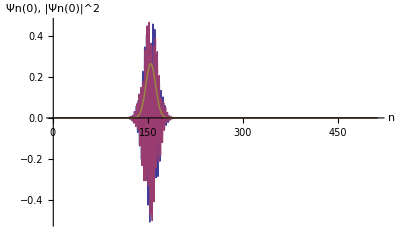

```mathematica
ListPlot[
{Re[Ψ0Array],Im[Ψ0Array],Ψ0Abs2Array},
Joined->True,
PlotRange->All,
AxesLabel->{"n","Ψn(0), |Ψn(0)|^2"}
]
```

```mathematica
(*
A function to get the numeric 2nd derivative of a set of points using FFTs
*)
```

```mathematica
FFTDerivativeKn2[s_]:=
(If[
s≤NN/2,
2*Pi*(s-1),
2*Pi*(s-1-NN)
]/LL)^2;
FFTDerivative2[fArray_]:=(
fArrayFFTForward=Fourier[fArray,FourierParameters->{1,-1}];
fArrayFFTForwardTimesIk2=fArrayFFTForward;
Do[
fArrayFFTForwardTimesIk2[[s]]*=-FFTDerivativeKn2[s],
{s,1,NN}
];
fArrayFFTForwardTimesIk2FFTInverse=InverseFourier[fArrayFFTForwardTimesIk2,FourierParameters->{1,-1}];
Return[fArrayFFTForwardTimesIk2FFTInverse];
)
```

```mathematica
(*
Now we need a function to act as the normalized hamiltonian operator on an array of complex values
*)
H[ϕArray_]:=-(ℏc^2/(2*m))*FFTDerivative2[ϕArray];
H[ϕArray_,VArray_]:=-(ℏc^2/(2*m))*FFTDerivative2[ϕArray]+VArray*ϕArray;
HNorm[ϕArray_]:=(2/ΔE)*(H[ϕArray]-(EMin+ΔE/2)*ϕArray);
HNorm[ϕArray_,VArray_]:=(2/ΔE)*(H[ϕArray,VArray]-(EMin+ΔE/2)*ϕArray);
```

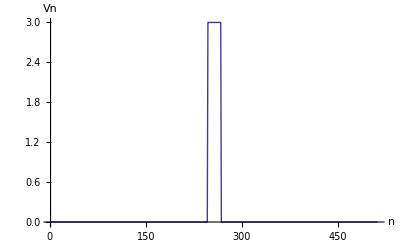

```mathematica
(*
Set up a potential function that is defined over the region xMin to xMax.
*)
(*VMax=6;*)
(*VThicknessFactor=.15;*)
(*V[x_]:=If[x<xMin+VThicknessFactor*LL||x>xMax-VThicknessFactor*LL,VMax,0];*)
VMax=3;
VThicknessFactor=.48;
V[x_]:=If[x<xMin+VThicknessFactor*LL||x>xMax-VThicknessFactor*LL,0,VMax];
VArray={};
For[n=1,n≤NN,n++,VArray=Append[VArray,V[xArray[[n]]]]];
VMin=Min[VArray];
ListPlot[
VArray,
Joined->True,
PlotRange->All,
AxesLabel->{"n","Vn"}
]
```

```mathematica
(*
Get the maximum value for the kinetic energy. Also find the minimum and maximum energy eigenvalues. Then use these to find an expression for t for the normalized H
*)
KMax =(Pi*ℏc*NN/LL)^2/(2*m);
EMax=KMax+VMax;(*Max[Abs[HNorm[Ψ0Array,VArray]^2]]*)
EMin=Min[0,VMin];
ΔE=EMax-EMin;
Print["KMax=",NumberForm[KMax,32]];
Print["EMax=",NumberForm[EMax,32]];
Print["EMin=",NumberForm[EMin,32]];
```

KMax=9.85740413756665

EMax=12.85740413756665

EMin=0

```mathematica
(*
Make the numerical estimation of the time evolution operator based on the chebyshev expansion of the analytical operator.
*)
U[Ψ0Array_,VArray_,t_]:=(

Print["dt=",t];
Print["EMin=",NumberForm[EMin,32]];
Print["ΔE=",NumberForm[ΔE,32]];

(* Initialize the new wave packet with all zeros*)
ΨtArray=Table[0,{NN}];

(* Calculate the α(t) for this evolution *)
α=(t*ΔE)/(2*ℏ);
Print["α=",NumberForm[α,32]];

(* Get the overal scaling factor λ(t) (that resulted from scaling H to Hnorm) *)
λExp=-t*(I/ℏc)*(ΔE/2+EMin);
λ=Exp[λExp];
Print["λExp=",NumberForm[λExp,32]];
Print["λ=",NumberForm[λ,32]];

(* Calculate the first two chebyshev operator "polynomials" *)
(*Print["Calculate the first two chebyshev operator polynomials"];*)
ϕ0Array=Ψ0Array;
ϕ1Array=-I*HNorm[Ψ0Array,VArray];
(*Print[MatrixForm[ϕ0Array]];*)
(*Print[MatrixForm[ϕ1Array]];*)


(* Make arrays that will hold the previous two ϕm values for the calculation of the next one *)
ϕmMinus1Array=ϕ1Array;
ϕmMinus2Array=ϕ0Array;

(* Calculate the number of terms to keep in the Chebyshev expansion *)
MM=Max[20,Ceiling[α+11.38*α^0.32]];
Print["MM=",MM];

(*Print["ψ0[",256,"] = ",NumberForm[Ψ0Array[[256]],20]];
Print["ψ0[",312,"] = ",NumberForm[Ψ0Array[[312]],20]];
Print[""];*)

(* Now we calculate and sum up all the terms in the expansion *)
For[mm=0,mm<MM,mm++,

(* Find the am, the mth coefficient in the expansion *)
(*Print["Finding a",mm];*)
am=BesselJ[mm,α]*If[mm==0,1,2];
(*Print["a",mm,"=",NumberForm[am,20]];*)

(* Get ϕm *)
(*Print["ϕ",mm-1,"[",256,"] = ",NumberForm[ϕmArray[[256]],20]];*)
ϕmArray=
If[mm==0,ϕ0Array,
If[mm==1,ϕ1Array,
ϕmArrayNew=-2*I*HNorm[ϕmMinus1Array,VArray]+ϕmMinus2Array;
ϕmMinus2Array=ϕmMinus1Array;
ϕmMinus1Array=ϕmArrayNew;
ϕmArrayNew
]
];
(*Print["ϕ",mm,"[",150,"] = ",NumberForm[ϕmArray[[150]],32]];*)
Print["am*ϕ",mm,"[",150,"] = ",NumberForm[am*ϕmArray[[150]],32]];

(* Add this component to the total wave packet accumulator *)
ΨtArray+=am*ϕmArray
(*Print["ΨtArray+am*ϕmArray",mm,"[",150,"] = ",NumberForm[ΨtArray[[150]],32]];*)
];

(*Print["Sum[150]=",NumberForm[ΨtArray[[150]],32]];*)

(* Multiply the entire sum by the HNorm scaling factor *)
ΨtArray*=λ;

Print["ψt[",150,"] = ",NumberForm[ΨtArray[[150]],20]];
(*Print["ψt[",312,"] = ",NumberForm[ΨtArray[[312]],20]];*)

(* Return the evolved wave packet *)
(*Print["ψ[",256,"] = ",NumberForm[ΨtArray[[256]],20]];*)
Return[ΨtArray];
);
```

```mathematica
ΨArray=Ψ0Array;
dt=1;
T=60;
plotArray={};
Do[
(
ΨArray=U[ΨArray,VArray,dt];
plot=ListPlot[{
Abs[Ψ0Array]^2,
Abs[ΨArray]^2,
VArray
},
Joined->True,
PlotRange->{{0,NN},{0,1}},
Filling->Axis
];
AppendTo[plotArray,plot];
),
{n,T}
]
ListAnimate[plotArray]
```

```mathematica
(* Output test comparison data for realtime sim *)
```

```mathematica
Ψ0Array[[150]]
```

-0.426487-0.200992 ⅈ

```mathematica
NumberForm[FFTDerivative2[Ψ0Array][[150]],32]
```

43.5290118115666+18.43282851671061 ⅈ

```mathematica
NumberForm[HNorm[Ψ0Array,VArray][[150]],32]
```

0.1685112015740519+0.0917491174730588 ⅈ

```mathematica
aaa=1.234567890+0.987654321I;
bbb=2.345678901+1.098765432I;
NumberForm[aaa*bbb,32]
NumberForm[aaa*λ,32]
```

1.810699424744857+3.673220423240359 ⅈ

1.266083803889342+0.946916434717508 ⅈ

```mathematica
Conjugate[1.2660838038893418+0.9469164347175083 ⅈ]
```

1.26608-0.946916 ⅈ

```mathematica
Ψ1Array=U[Ψ0Array, VArray, 1.0];
(*NumberForm[Ψ1Array[[150]],32]
Ψ1ArrayAbs2=Abs[Ψ1Array]^2;
NumberForm[Ψ1ArrayAbs2[[150]],32]
NumberForm[Sum[Ψ1ArrayAbs2[[i]],{i,1,NN}]*(LL/NN),32]*)
```

dt=1.

EMin=0

ΔE=12.85740413756665

α=9.76691864317238

λExp=0.-0.03257893380083757 ⅈ

λ=0.999469353473798-0.03257317096426748 ⅈ

MM=34

am*ϕ0[150] = 0.097696531759068+0.04604172700264225 ⅈ

am*ϕ1[150] = 0.01849648494126897-0.03397160635648433 ⅈ

am*ϕ2[150] = -0.1454297566610444-0.05859138188479309 ⅈ

am*ϕ3[150] = 0.0005843157311501173-0.001162180071715977 ⅈ

am*ϕ4[150] = -0.01176686224767637-0.03157239600378142 ⅈ

am*ϕ5[150] = -0.0579521279211924+0.1508937748561033 ⅈ

am*ϕ6[150] = 0.02390885892508024+0.01475326217831343 ⅈ

am*ϕ7[150] = -0.01562899211949952-0.05775595959908473 ⅈ

am*ϕ8[150] = 0.2493991366967306+0.1049887389997911 ⅈ

am*ϕ9[150] = -0.097024679192633+0.1048559862845808 ⅈ

am*ϕ10[150] = 0.0823543590473748+0.002167101587575567 ⅈ

am*ϕ11[150] = -0.03784003579535412+0.07412035946190974 ⅈ

am*ϕ12[150] = -0.006443707282345361-0.01576016185122557 ⅈ

am*ϕ13[150] = -0.002054925868117764+0.01294902639914018 ⅈ

am*ϕ14[150] = -0.005008568119869051-0.003401929030826772 ⅈ

am*ϕ15[150] = 0.0007718179421679583+0.0003444742246286505 ⅈ

am*ϕ16[150] = -0.0006533023344063694-0.0001808513839777819 ⅈ

am*ϕ17[150] = 0.0001252540334268556-0.0001223779069555666 ⅈ

am*ϕ18[150] = -0.00002704814309409765+0.00001497919759033792 ⅈ

am*ϕ19[150] = 6.043940976084468×10^-6-0.00001448795993504445 ⅈ

am*ϕ20[150] = 1.112741985430795×10^-6+(2.288431134663349×10^-6) ⅈ

am*ϕ21[150] = -1.046241854222663×10^-7-(6.135031916890324×10^-7) ⅈ

am*ϕ22[150] = 1.637196400558008×10^-7+(1.003220367713839×10^-7) ⅈ

am*ϕ23[150] = -2.295948894756632×10^-8-(5.770250235111795×10^-10) ⅈ

am*ϕ24[150] = 6.801376751457633×10^-9+(3.480739271125668×10^-10) ⅈ

am*ϕ25[150] = -9.40633398032926×10^-10+(1.008539645431051×10^-9) ⅈ

am*ϕ26[150] = 8.43577487227649×10^-11-(1.332832567388676×10^-10) ⅈ

am*ϕ27[150] = -1.041540031596154×10^-11+(4.297124058275496×10^-11) ⅈ

am*ϕ28[150] = -3.327818219112366×10^-12-(5.382767864517551×10^-12) ⅈ

am*ϕ29[150] = 4.485918122410246×10^-13+(6.990960779296834×10^-13) ⅈ

am*ϕ30[150] = -1.667552836998861×10^-13-(7.553851523683591×10^-14) ⅈ

am*ϕ31[150] = 1.977162052623165×10^-14-(4.179801259974401×10^-15) ⅈ

am*ϕ32[150] = -2.986687663379233×10^-15+(7.707155588413609×10^-16) ⅈ

am*ϕ33[150] = 3.02347785566005×10^-16-(4.122465758537902×10^-16) ⅈ

ψt[150] = 0.1035163405993156+0.3053880717374624 ⅈ

```mathematica
ΨArray=Ψ0Array;
dt=1;
T=60;
plotArray={};
Do[
(
ΨArray=U[ΨArray,VArray,dt];
AbsΨSq =Abs[ΨArray]^2;
Normalization=0;
For[i=1,i≤NN,i++,Normalization+=AbsΨSq[[i]]];
Normalization *=LL/NN;
Print["n=",n];
Print["AbsΨSq[150]=",NumberForm[AbsΨSq[[150]],32]];
Print["Norm=",NumberForm[Normalization,32]];
(*Print[StringJoin[
"t:",n,
" x:",150,
"Abs[Psi]^2: ",[Abs[ΨArray]^2][150]]
];*)
),
{n,T}
]
```